```mathematica
Integrate[p^2(Q+p)^2 Exp[-p/T],{p,0,Infinity}]
```

ConditionalExpression[2 T^3 (Q^2+6 Q T+12 T^2), Re[T]>0]

```mathematica
a=255/(1.13 *886.7)
```

0.254498

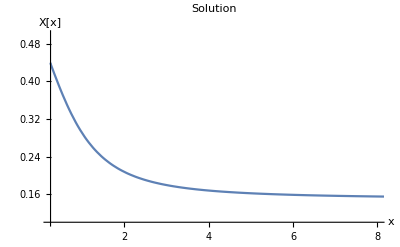

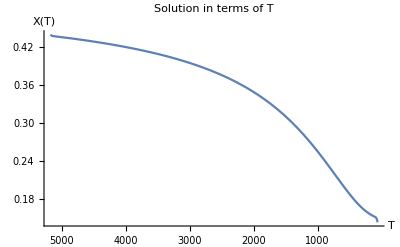

```mathematica
eqn=y'[x]==a (12+6x+x^2)/x^4(E^-x-y[x](1+E^-x));

sol=NDSolve[{eqn,y[0.25]==0.44},y,{x,0.25,10}];
Plot[Evaluate[y[x]/. sol],{x,0.25,20},PlotRange->{{0.25,8},{0.1,0.5}},AxesLabel->{"x","X[x]"},PlotLabel->"Solution"]
xAsFunctionOfT[T_]:=1293/T;
yAsFunctionOfT[T_]:=y[x]/. sol/. x->xAsFunctionOfT[T];
Plot[Evaluate[yAsFunctionOfT[T]],{T,1293/20,1293/0.25},PlotRange->{{1293/20,1293/0.25},{0.1,0.5}},ScalingFunctions->{"Reverse",Identity},AxesLabel->{"T","X(T)"},PlotLabel->"Solution in terms of T"]
```

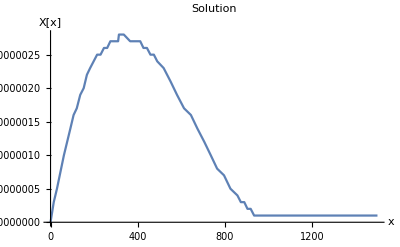

```mathematica
eqn=y'[x]==10^-15 √x Exp[-x](1-(1+4/3 √(2/Pi)x^(-3/2)Exp[x])y[x]);

sol=NDSolve[{eqn,y[0.01]==0.0001},y,{x,0.01,10000}];
Plot[Evaluate[y[x]/. sol],{x,0,1500},PlotRange->All,AxesLabel->{"x","X[x]"},PlotLabel->"Solution"]
```

```mathematica
Subscript[n, s]=(Subscript[g, s] 4Pi)/(2Pi)^3 Integrate[ e √(e^2-m^2) Exp[-e/T],{e,m,Infinity},Assumptions->{m>0,T>0}]
```

(m^2 T BesselK[2,m/T] g_s)/(2 π^2)

(m^2 T g_s)/(π^2 x^2)-(m^2 T g_s)/(4 π^2)+O[x]^2

ⅇ^(-x+O[1/x]^2) ((m^2 T g_s √(1/x))/(2 √2 π^(3/2))+O[1/x]^(3/2))

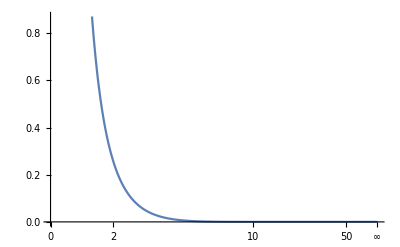

```mathematica
Subscript[n, UR]=(m^2 T  Subscript[g, s])/(2 π^2)Series[BesselK[2,x],{x,0,1}]
Subscript[n, NR]=(m^2 T  Subscript[g, s])/(2 π^2)Series[BesselK[2,x],{x,Infinity,1}]
Plot[BesselK[2,x],{x,0,Infinity}]
```

```mathematica
Subscript[n, UR]=(T^3 Subscript[g, s])/π^2
Subscript[n, NR]= Subscript[g, s] (mT/(2π))^(3/2)Exp[-m/T]
```

```mathematica
A=1.719482286206256*^-28
```

1.71948×10^-28

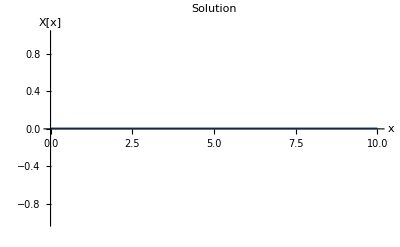

```mathematica
eqn=y'[x]==10^-28 √x Exp[-x](1-(1+4/3 √(2/Pi)x^(-3/2)Exp[x])y[x]);

sol=NDSolve[{eqn,y[0.001]==0.005},y,{x,0.0001,10}];
Plot[Evaluate[y[x]/. sol],{x,0,10},PlotRange->All,AxesLabel->{"x","X[x]"},PlotLabel->"Solution"]
```

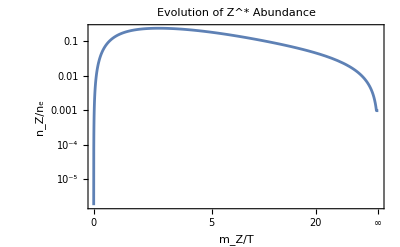

```mathematica
eqn=y'[x]==√x Exp[-x](1-(1+4/3 √(2/Pi)x^(-3/2)Exp[x])y[x]);
sol=NDSolve[{eqn,y[0.1]==0.011398},y,{x,0.01,100000}];
LogPlot[Evaluate[y[x]/. sol],{x,0,Infinity},PlotRange->All,Frame->True,FrameLabel->{"m_Z/T","n_Z/n_e"},PlotLabel->"Evolution of Z^* Abundance"]
```